```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/godfather/Documents/TaskDash/Boundary/separation

```mathematica
fo = Import["exp_fo.txt","Table"][[12;;]];
xh = Import["exp_xh.txt","Table"][[12;;]];
```

```mathematica
fo = ({fo[[1]],fo[[#]]})ᵀ&/@Range[2,4];
xh =({xh[[1]],xh[[#]] })ᵀ&/@Range[2,4];
```

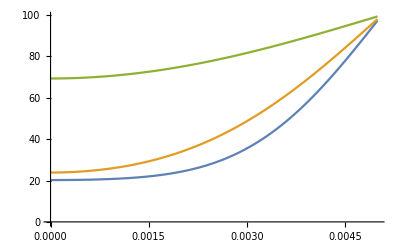

```mathematica
ListPlot[fo, Joined->True]
```

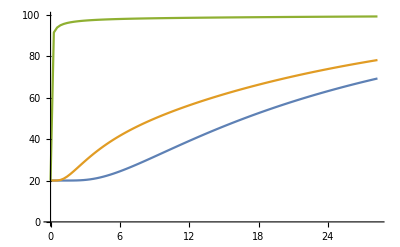

```mathematica
ListPlot[xh, Joined->True]
```